```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0.gpl,surface1.gpl,surface2.gpl,surface3.gpl}

{{150,3.62733×10^7},{200,3.17063×10^7},{250,2.83923×10^7},{300,2.602×10^7}}

{{150,362.733},{200,317.063},{250,283.923},{300,260.2}}

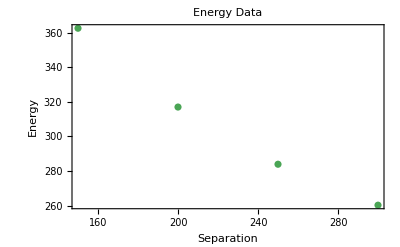

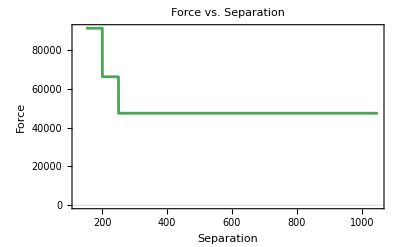

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
const double neumann_value=-tan(theta);//(exactish_solution.gradient(fe_face_values.quadrature_point(q_point))*fe_face_values.normal_vector(q_point));
```

```mathematica
const double neumann_value=-tan(theta);//(exactish_solution.gradient(fe_face_values.quadrature_point(q_point))*fe_face_values.normal_vector(q_point));
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterizationconst double neumann_value=-tan(theta);//(exactish_solution.gradient(fe_face_values.quadrature_point(q_point))*fe_face_values.normal_vector(q_point));/BoundaryValues"];
Export["energyGraphnice.jpg", energyGraphnice, ImageResolution->1200]
```

energyGraphnice.jpg

```mathematica
"energyGraphnice.jpg"
```

energyGraphnice.jpg

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["energyGraphnice.png"]]]
```

AbsoluteFileName::fdnfnd: Directory or file energyGraphnice.png not found.

DirectoryName::string: String expected at position 1 in DirectoryName[$Failed].

SystemOpen[DirectoryName[$Failed]]

```mathematica
prettySurface[filename_] :=const double neumann_value=-tan(theta);//(exactish_solution.gradient(fe_face_values.quadrature_point(q_point))*fe_face_values.normal_vector(q_point));
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface3.gpl"]
```

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface0.gpl"]
```

-Graphics3D-

```mathematica
|
```